```mathematica
<<xlr8r.m
```

xCellerator 0.90 (26-Oct-2012) loaded Fri 2 Nov 2012 12:55:11
using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4)
using MathSBML version 2.12

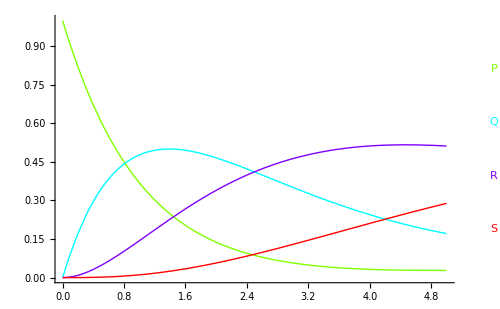

```mathematica
eqs={{P-> Q, 1}, {Q-> R, .5}, {R->S, .2}, {S-> P, .1}};
n=run[eqs,{0,5}, "IC"-> {P-> 1, Q-> 0, S-> 0}]; 
runPlot[n,ImageSize-> 500]
```

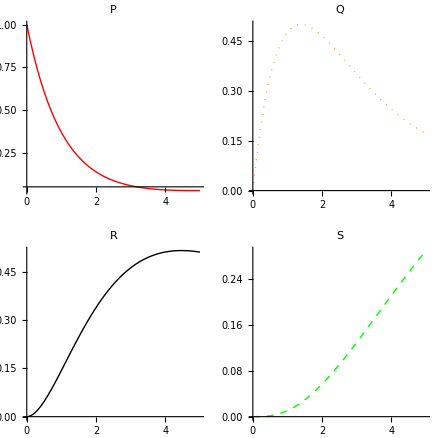

```mathematica
gridPlot[n,"Columns"-> 2, "Width"-> 200, "Aspect"-> 1, "styles"-> {Directive[Red,Thick], Directive[Orange,Dotted], Black, Directive[Green,Thick,Dashed]}]
```